```mathematica
binpath = FileNameJoin[{NotebookDirectory[],"chooser","bin","vis.exe"}];
```

```mathematica
RunAggSim[23, {{2,3},{4,7}}]
```

C:\Users\Pietro\Desktop\Projects\Wolfram\WSS23_AggSystems\chooser\bin\vis.exe "23" "{{2, 3}, {4, 7}}"

0

C:\Users\Pietro\Desktop\Projects\Wolfram\WSS23_AggSystems\chooser\bin\vis.exe "23" "{{2, 3}, {4, 7}}"

0

```mathematica
RunAggSim[rule_Integer, initial_List] :=Module[{
binpath = FileNameJoin[{NotebookDirectory[],"chooser","bin","vis.exe"}]
},
Parametrize[str_] := StringJoin["\"",ToString@str,"\""];
Run@(StringRiffle[{binpath, Parametrize@rule, Parametrize@initial}," "] // Echo)
]
```

```mathematica
RunAggSim[rule_Integer, initial_List] := StringRiffle[ToString /@ {binpath, rule,initial}, " "]
```

```mathematica
Run @ StringJoin[FileNameJoin[{NotebookDirectory[],"test_call.exe"}], " 242 {{1,0},{0,1}}"]
```

-1073741510

```mathematica
Run["start C:\\Users\\Pietro\\Desktop\\Projects\\Wolfram\\WSS23_AggSystems\\chooser\\bin\\vis.exe \"23\" \"{{2, 3}, {4, 7}}\""]
```

0

```mathematica
StringJoin[FileNameJoin[{NotebookDirectory[],"test_call.exe"}], " 242 {{1,0},{0,1}}"]
```

C:\Users\Pietro\Desktop\Projects\Wolfram\WSS23_AggSystems\test_call.exe 242 {{1,0},{0,1}}

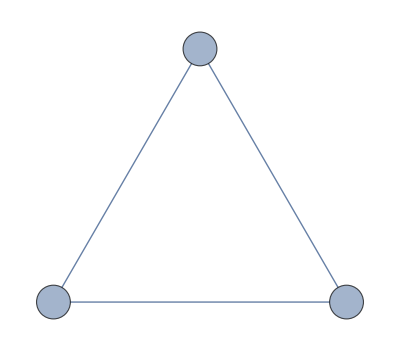

-Graphics-

Clicked on vertex First[2]

Clicked on vertex First[2]

```mathematica
graph=Graph[{1,2,3},{1<->2,2<->3,3<->1},VertexShapeFunction->(EventHandler[Disk[#1,0.1],"MouseClicked":>Print["Clicked on vertex ",First[#2]]]&)]

Show[graph]
```